## PREPARATIONS

```mathematica
Off[General::spell];
WorkDirNum="c/exe/parton/transversity/input_saman/";
```

## INPUTS FROM MODEL CALCULATION

## Results evolved to Q2=28 GeV^2

PROTON

```mathematica
intorder=3;
```

### Initial scale for the proton calculated at LO by requiring <x>=0.36 at 10 GeV^2 and using MTRW parameters

```mathematica
(* alpha(Mz)=0.13939  - Q2_0=0.176872  alpha(Q2_0)=4.4294539514500872*)
```

### input x f1(x) of the PROTON from the model evolved at LO to Q^2=28 GeV^2

```mathematica
list0i:=ReadList[StringJoin[WorkDirNum,"x_f1_lo_up_q2_28p0_schlumpf.dat"],{Number,Number,Number,Number,Number}];
f1ulist=Table[{list0i[[n,1]],list0i[[n,4]]},{n,Length[list0i]}];
xf1upr :=Interpolation[f1ulist,InterpolationOrder->intorder];  
f1ubarlist=Table[{list0i[[n,1]],list0i[[n,5]]},{n,Length[list0i]}];

xf1ubarpr= Interpolation[f1ubarlist,InterpolationOrder->intorder];  
list02:=ReadList[StringJoin[WorkDirNum,"x_f1_lo_down_q2_28p0_schlumpf.dat"],{Number,Number,Number,Number,Number}];
f1dlist=Table[{list02[[n,1]],list02[[n,4]]},{n,Length[list02]}];
xf1dpr= Interpolation[f1dlist,InterpolationOrder->intorder];  
f1dbarlist=Table[{list02[[n,1]],list02[[n,5]]},{n,Length[list02]}];
xf1dbarpr= Interpolation[f1dbarlist,InterpolationOrder->intorder];
```

```mathematica
list0i:=ReadList[StringJoin[WorkDirNum,"x_f1_lo_up_q2_28p0_diquark_gamberg.dat"],{Number,Number,Number,Number,Number}];
f1ulistg=Table[{list0i[[n,1]],list0i[[n,4]]},{n,Length[list0i]}];
xf1uprg :=Interpolation[f1ulistg,InterpolationOrder->intorder];  
f1ubarlistg=Table[{list0i[[n,1]],list0i[[n,5]]},{n,Length[list0i]}];
xf1ubarprg= Interpolation[f1ubarlistg,InterpolationOrder->intorder];  

list02:=ReadList[StringJoin[WorkDirNum,"x_f1_lo_down_q2_28p0_diquark_gamberg.dat"],{Number,Number,Number,Number,Number}];
f1dlistg=Table[{list02[[n,1]],list02[[n,4]]},{n,Length[list02]}];
xf1dprg= Interpolation[f1dlistg,InterpolationOrder->intorder];  
f1dbarlistg=Table[{list02[[n,1]],list02[[n,5]]},{n,Length[list02]}];
xf1dbarprg= Interpolation[f1dbarlistg,InterpolationOrder->intorder];
```

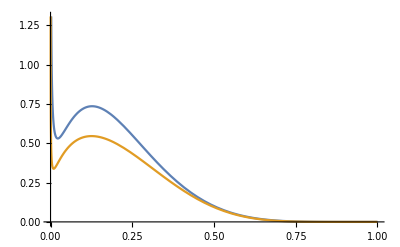

```mathematica
Plot[{xf1upr[x],xf1uprg[x]},{x,0,1}]
```

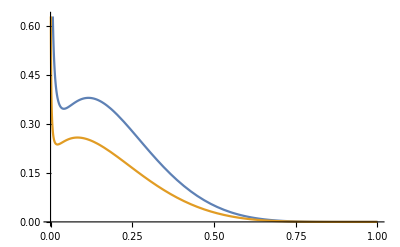

```mathematica
Plot[{xf1dpr[x],xf1dprg[x]},{x,0,1}]
```

### input x*(first moment in ksq/(2M^2) of SIVERS ) of the PROTON from the model evolved at LO to Q^2=28 GeV^2

```mathematica
(* the constant 20.14729318302453 is g^2=alpha_s*(4*Pi) at the scale of the model with alpha-S CALCULATED AT NLO (see pag. 8 of PRD90. The minus sign it is because the calculation is done for SIDIS.*)
```

```mathematica
list2:=ReadList[StringJoin[WorkDirNum,"x_first_moment_sivers_lo_ns_up_q2_28p0_schlumpf_mtrw_newm.dat"],{Number,Number,Number,Number,Number}];
siversulist=Table[{list2[[n,1]],-20.14729318302453*list2[[n,2]]},{n,Length[list2]}];
xsiversupr :=Interpolation[siversulist,InterpolationOrder->intorder];  
xsiversubarpr[x_]:=0.
list3:=ReadList[StringJoin[WorkDirNum,"x_first_moment_sivers_lo_ns_down_q2_28p0_schlumpf_mtrw_newm.dat"],{Number,Number,Number,Number,Number}];
siversdlist=Table[{list3[[n,1]],-20.14729318302453*list3[[n,2]]},{n,Length[list3]}];
xsiversdpr= Interpolation[siversdlist,InterpolationOrder->intorder];  
xsiversdbarpr[x_]:=0.
```

```mathematica
list2g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_sivers_lo_ns_up_q2_28p0_diquark_gamberg_mtrw_newm.dat"],{Number,Number,Number,Number,Number}];
siversulistg=Table[{list2g[[n,1]],-list2g[[n,2]]},{n,Length[list2g]}];
xsiversuprg :=Interpolation[siversulistg,InterpolationOrder->intorder];  
xsiversubarprg[x_]:=0.
list3g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_sivers_lo_ns_down_q2_28p0_diquark_gamberg_mtrw_newm.dat"],{Number,Number,Number,Number,Number}];
siversdlistg=Table[{list3g[[n,1]],-list3g[[n,2]]},{n,Length[list3g]}];
xsiversdprg= Interpolation[siversdlistg,InterpolationOrder->intorder];  
xsiversdbarprg[x_]:=0.
```

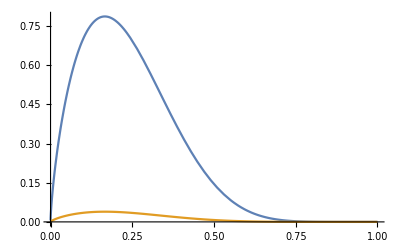

```mathematica
Plot[{xsiversupr[x],xsiversuprg[x]},{x,0,1}]
```

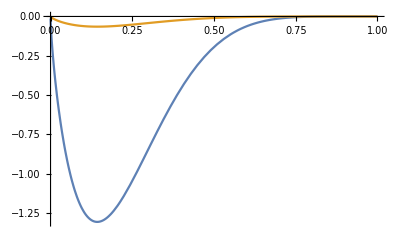

```mathematica
Plot[{xsiversdpr[x],xsiversdprg[x]},{x,0,1}]
```

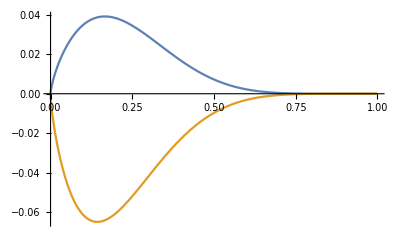

```mathematica
Plot[{xsiversuprg[x],xsiversdprg[x]},{x,0,1}]
```

### input x*(first moment in ksq/(2M^2) of Boer-Mulders ) of the PROTON from the model evolved at LO to Q^2=28 GeV^2

```mathematica
(* the constant 20.14729318302453 is g^2=alpha_s*(4*Pi) at the scale of the model with alpha-S CALCULATED AT NLO (see pag. 8 of PRD90. The minus sign it is because the calculation is done for SIDIS.*)
```

```mathematica
list8:=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_up_lo_q2_28p0.dat"],{Number,Number}];
xbmfmuprlist=Table[{list8[[n,1]],-20.14729318302453*list8[[n,2]]},{n,Length[list8]}];
xbmfmupr= Interpolation[xbmfmuprlist,InterpolationOrder->intorder];  
list9:=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_down_lo_q2_28p0.dat"],{Number,Number}];
xbmfmdprlist=Table[{list9[[n,1]],-20.14729318302453*list9[[n,2]]},{n,Length[list9]}];
xbmfmdpr= Interpolation[xbmfmdprlist,InterpolationOrder->intorder];  
xbmfmubarpr[x_]:=0
xbmfmdbarpr[x_]:=0
```

```mathematica
list8g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_up_lo_q2_28p0_diquark_gamberg_mtrw_newm.dat"],{Number,Number}];
xbmfmuprlistg=Table[{list8g[[n,1]],-list8g[[n,2]]},{n,Length[list8g]}];
xbmfmuprg= Interpolation[xbmfmuprlistg,InterpolationOrder->intorder];  
list9g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_down_lo_q2_28p0_diquark_gamberg_mtrw_newm.dat"],{Number,Number}];
xbmfmdprlistg=Table[{list9g[[n,1]],-list9g[[n,2]]},{n,Length[list9g]}];
xbmfmdprg= Interpolation[xbmfmdprlistg,InterpolationOrder->intorder];  
xbmfmubarprg[x_]:=0
xbmfmdbarprg[x_]:=0
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

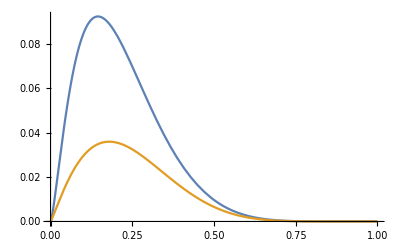

```mathematica
Plot[{xbmfmupr[x],xbmfmuprg[x]},{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

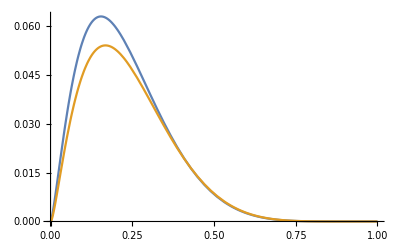

```mathematica
Plot[{xbmfmdpr[x],xbmfmdprg[x]},{x,0,1}]
```

### input x*(transversity) of the PROTON from the model evolved at LO to Q^2=28 GeV^2 - MISSING INPUT FROM DIQUARK MODEL

```mathematica
list10:=ReadList[StringJoin[WorkDirNum,"x_h1_up_lo_q2_28p0.dat"],{Number,Number}];
xh1uprlist=Table[{list10[[n,1]],list10[[n,2]]},{n,Length[list10]}];
xh1upr= Interpolation[xh1uprlist,InterpolationOrder->intorder];  
list11:=ReadList[StringJoin[WorkDirNum,"x_h1_down_lo_q2_28p0.dat"],{Number,Number}];
xh1dprlist=Table[{list11[[n,1]],list11[[n,2]]},{n,Length[list11]}];
xh1dpr= Interpolation[xh1dprlist,InterpolationOrder->intorder];  
xh1ubarpr[x_]:=0
xh1dbarpr[x_]:=0
```

### input x*(second moment in ksq/(2M^2) of pretzelosity) of the PROTON from the model evolved at LO to Q^2=28 GeV^2- MISSING INPUT FROM DIQUARK MODEL

```mathematica
list12:=ReadList[StringJoin[WorkDirNum,"x_second_moment_h1t_perp_up_lo_q2_28p0.dat"],{Number,Number}];
xsmpretuprlist=Table[{list12[[n,1]],list12[[n,2]]},{n,Length[list12]}];
xsmpretzelu= Interpolation[xsmpretuprlist,InterpolationOrder->intorder];  
list13:=ReadList[StringJoin[WorkDirNum,"x_second_moment_h1t_perp_down_lo_q2_28p0.dat"],{Number,Number}];
xsmpretdprlist=Table[{list13[[n,1]],list13[[n,2]]},{n,Length[list13]}];
xsmpretzeld= Interpolation[xsmpretdprlist,InterpolationOrder->intorder];  
xsmpretzelubar[x_]:=0
xsmpretzeldbar[x_]:=0
```

### input x*(first moment in ksq/(2M^2) of H1L^perp) of the PROTON from the model evolved at LO to Q^2=28 GeV^2

```mathematica
list14:=ReadList[StringJoin[WorkDirNum,"x_first_moment_h1L_perp_up_lo_q2_28p0.dat"],{Number,Number}];
xfmh1lulist=Table[{list14[[n,1]],list14[[n,2]]},{n,Length[list14]}];
xfmh1lu= Interpolation[xfmh1lulist,InterpolationOrder->intorder];  
list15:=ReadList[StringJoin[WorkDirNum,"x_first_moment_h1L_perp_down_lo_q2_28p0.dat"],{Number,Number}];
xfmh1ldlist=Table[{list15[[n,1]],list15[[n,2]]},{n,Length[list15]}];
xfmh1ld= Interpolation[xfmh1ldlist,InterpolationOrder->intorder];  
xfmh1lubar[x_]:=0
xfmh1ldbar[x_]:=0
```

```mathematica
list14g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_h1L_perp_up_lo_q2_28p0_diquark_gamberg.dat"],{Number,Number}];
xfmh1lulistg=Table[{list14g[[n,1]],list14g[[n,2]]},{n,Length[list14g]}];
xfmh1lug= Interpolation[xfmh1lulistg,InterpolationOrder->intorder];  
list15g:=ReadList[StringJoin[WorkDirNum,"x_first_moment_h1L_perp_down_lo_q2_28p0_diquark_gamberg.dat"],{Number,Number}];
xfmh1ldlistg=Table[{list15g[[n,1]],list15g[[n,2]]},{n,Length[list15g]}];
xfmh1ldg= Interpolation[xfmh1ldlistg,InterpolationOrder->intorder];  
xfmh1lubarg[x_]:=0
xfmh1ldbarg[x_]:=0
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

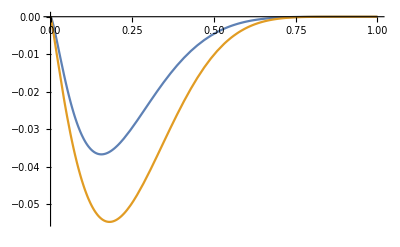

```mathematica
Plot[{xfmh1lu[x],xfmh1lug[x]},{x,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

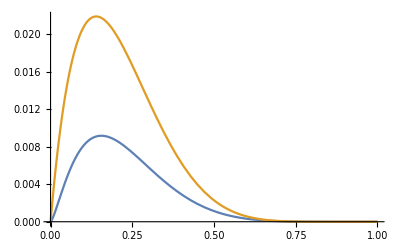

```mathematica
Plot[{xfmh1ld[x],xfmh1ldg[x]},{x,0,1}]
```

PION

```mathematica
(* alpha(Mz)=0.13939  - Q2_0=0.2115  alpha(Q2_0)/(4*Pi)=0.225*)
```

```mathematica
(*the distributions refer to the charge pions:
```

### input x f1(x) of the PION from the model evolved at LO to Q^2=28 GeV^2- MISSING INPUT FROM DIQUARK MODEL

```mathematica
list1=ReadList[StringJoin[WorkDirNum,"x_f1_lo_up_q2_28p0_pion_mtrw_newm.dat"],
{Number,Number,Number,Number,Number}];
listf1u=Table[{list1[[n,1]],list1[[n,4]]},{n,Length[list1]}];
listf1ubar=Table[{list1[[n,1]],list1[[n,5]]},{n,Length[list1]}];
xf1ubarpion= Interpolation[listf1ubar,InterpolationOrder->intorder];  
xf1upion:=Interpolation[listf1u,InterpolationOrder->intorder];  
xf1dpion[x_]:=xf1ubarpion
xf1dbarpion[x_]:=xf1upion
```

```mathematica
(*ubar and d for pi^-; u and dbar for pi^+ *)
```

### input x*(first moment in ksq/2M^2 h1^perp(x) ) of the PION from the model evolved at LO to Q^2=28 GeV^2

```mathematica
(* the constant 14.815799083528919 is g^2=alpha_s*(4*Pi) at the scale of the model with alpha-S CALCULATED AT NLO (see pag. 8 of PRD90. The minus sign it is because the calculation is done for SIDIS.*)
```

```mathematica
list2=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_up_lo_q2_28p0_pion_mtrw_newm.dat"],
{Number,Number}];
xbmfmubarpionlist=Table[{list2[[n,1]],-list2[[n,2]]*14.815799083528919},{n,Length[list2]}];
xbmfmubarpion= Interpolation[xbmfmubarpionlist,InterpolationOrder->intorder];
```

```mathematica
list2g=ReadList[StringJoin[WorkDirNum,"x_first_moment_bm_up_lo_q2_28p0_pion_diquark_gamberg_mtrw_newm.dat"],
{Number,Number}];
xbmfmubarpionlistg=Table[{list2g[[n,1]],-list2g[[n,2]]},{n,Length[list2g]}];
xbmfmubarpiong= Interpolation[xbmfmubarpionlistg,InterpolationOrder->intorder];
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

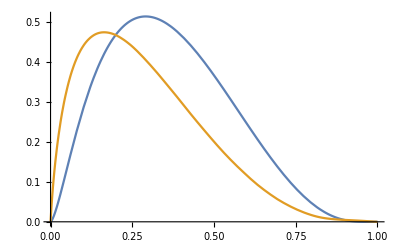

```mathematica
Plot[{xbmfmubarpion[x],xbmfmubarpiong[x]},{x,0,1}]
```